# Preparation

## Dataset

```mathematica
linearDS=Dataset[{<|"Nodes Count"->5,"Oracle Queries"->2,"Separator MSE"->0.8060,"Random MSE"->0.2731|>,<|"Nodes Count"->5,"Oracle Queries"->2,"Separator MSE"->0.1093,"Random MSE"->0.2562|>,<|"Nodes Count"->5,"Oracle Queries"->2,"Separator MSE"->1.2802,"Random MSE"->0.0530|>,<|"Nodes Count"->5,"Oracle Queries"->2,"Separator MSE"->0.7525,"Random MSE"->0.1783|>,<|"Nodes Count"->5,"Oracle Queries"->2,"Separator MSE"->1.2393,"Random MSE"->0.4292|>,<|"Nodes Count"->10,"Oracle Queries"->3,"Separator MSE"->5.6163,"Random MSE"->1.1244|>,<|"Nodes Count"->10,"Oracle Queries"->3,"Separator MSE"->1.6236,"Random MSE"->0.1243|>,<|"Nodes Count"->10,"Oracle Queries"->3,"Separator MSE"->1.9100,"Random MSE"->0.3328|>,<|"Nodes Count"->10,"Oracle Queries"->3,"Separator MSE"->6.6607,"Random MSE"->0.5401|>,<|"Nodes Count"->10,"Oracle Queries"->3,"Separator MSE"->2.9670,"Random MSE"->0.3051|>,<|"Nodes Count"->15,"Oracle Queries"->4,"Separator MSE"->9.2862,"Random MSE"->0.2709|>,<|"Nodes Count"->15,"Oracle Queries"->4,"Separator MSE"->4.0269,"Random MSE"->0.7240|>,<|"Nodes Count"->15,"Oracle Queries"->4,"Separator MSE"->5.8952,"Random MSE"->0.8527|>,<|"Nodes Count"->15,"Oracle Queries"->4,"Separator MSE"->8.6131,"Random MSE"->0.3333|>,<|"Nodes Count"->15,"Oracle Queries"->4,"Separator MSE"->1.7551,"Random MSE"->1.2544|>,<|"Nodes Count"->25,"Oracle Queries"->5,"Separator MSE"->16.1916,"Random MSE"->1.1110|>,<|"Nodes Count"->25,"Oracle Queries"->5,"Separator MSE"->7.8161,"Random MSE"->0.5087|>,<|"Nodes Count"->25,"Oracle Queries"->5,"Separator MSE"->5.0618,"Random MSE"->3.0661|>,<|"Nodes Count"->25,"Oracle Queries"->5,"Separator MSE"->6.1072,"Random MSE"->1.1034|>,<|"Nodes Count"->25,"Oracle Queries"->5,"Separator MSE"->5.3996,"Random MSE"->0.2384|>,<|"Nodes Count"->50,"Oracle Queries"->7,"Separator MSE"->31.2572,"Random MSE"->5.5034|>,<|"Nodes Count"->50,"Oracle Queries"->7,"Separator MSE"->35.2181,"Random MSE"->6.4097|>,<|"Nodes Count"->50,"Oracle Queries"->7,"Separator MSE"->29.1011,"Random MSE"->4.9452|>,<|"Nodes Count"->50,"Oracle Queries"->7,"Separator MSE"->10.3335,"Random MSE"->2.1321|>,<|"Nodes Count"->50,"Oracle Queries"->7,"Separator MSE"->12.2552,"Random MSE"->2.1503|>,<|"Nodes Count"->100,"Oracle Queries"->10,"Separator MSE"->17.0418,"Random MSE"->4.5761|>,<|"Nodes Count"->100,"Oracle Queries"->10,"Separator MSE"->28.2113,"Random MSE"->8.9788|>,<|"Nodes Count"->100,"Oracle Queries"->10,"Separator MSE"->34.5643,"Random MSE"->4.1719|>,<|"Nodes Count"->100,"Oracle Queries"->10,"Separator MSE"->87.2323,"Random MSE"->19.4754|>,<|"Nodes Count"->100,"Oracle Queries"->10,"Separator MSE"->43.5559,"Random MSE"->9.6935|>,<|"Nodes Count"->150,"Oracle Queries"->13,"Separator MSE"->46.664,"Random MSE"->18.3080|>,<|"Nodes Count"->150,"Oracle Queries"->13,"Separator MSE"->30.2776,"Random MSE"->10.2368|>,<|"Nodes Count"->150,"Oracle Queries"->13,"Separator MSE"->30.1979,"Random MSE"->2.4806|>,<|"Nodes Count"->150,"Oracle Queries"->13,"Separator MSE"->51.8355,"Random MSE"->2.8703|>,<|"Nodes Count"->150,"Oracle Queries"->13,"Separator MSE"->57.5102,"Random MSE"->8.5202|>,<|"Nodes Count"->250,"Oracle Queries"->16,"Separator MSE"->214.08801,"Random MSE"->11.0693|>,<|"Nodes Count"->250,"Oracle Queries"->16,"Separator MSE"->86.9779,"Random MSE"->11.0081|>,<|"Nodes Count"->250,"Oracle Queries"->16,"Separator MSE"->86.7803,"Random MSE"->8.1785|>,<|"Nodes Count"->250,"Oracle Queries"->16,"Separator MSE"->102.2110,"Random MSE"->17.8288|>,<|"Nodes Count"->250,"Oracle Queries"->16,"Separator MSE"->221.9190,"Random MSE"->30.1453|>,<|"Nodes Count"->500,"Oracle Queries"->23,"Separator MSE"->272.1650,"Random MSE"->45.4500|>,<|"Nodes Count"->500,"Oracle Queries"->23,"Separator MSE"->152.5000,"Random MSE"->28.6039|>,<|"Nodes Count"->500,"Oracle Queries"->23,"Separator MSE"->354.3140,"Random MSE"->27.7933|>,<|"Nodes Count"->500,"Oracle Queries"->23,"Separator MSE"->280.4160,"Random MSE"->38.1420|>,<|"Nodes Count"->500,"Oracle Queries"->23,"Separator MSE"->358.8710,"Random MSE"->18.5066|>}]
```

## Prelim Tests

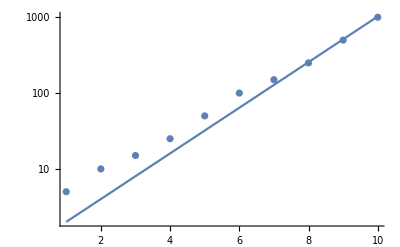

```mathematica
Show[LogPlot[2^x,{x,1,10}],ListLogPlot[{5,10,15,25,50,100,150,250,500,1000}],PlotRange->All]
```

# Usage

## Cleaning

```mathematica
meansDS=linearDS[GroupBy["Nodes Count"],Mean]
```

```mathematica
sepValues=Values[List@@meansDS[[All,{"Nodes Count","Separator MSE"}]]]//Normal;
rndValues=Values[List@@meansDS[[All,{"Nodes Count","Random MSE"}]]]//Normal;
```

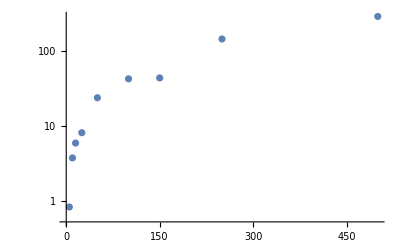

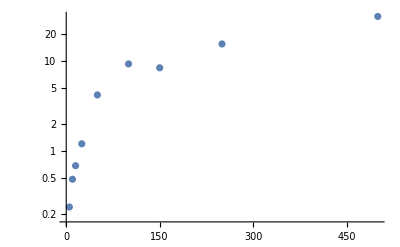

```mathematica
lplot=ListLogPlot[sepValues]
rplot=ListLogPlot[rndValues]
```

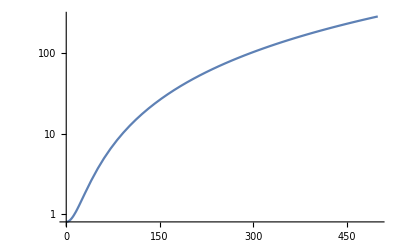

```mathematica
With[{expr=(a x^2+b)/.With[{first=First[sepValues],last=Last[sepValues]},With[{x1=First[first],y1=Last[first],xn=First[last],yn=Last[last]},Solve[{a x1^2+b==y1,a xn^2+b==yn},{a,b}]]][[1]]},refplot=LogPlot[Evaluate[expr],{x,0,500}]]
```

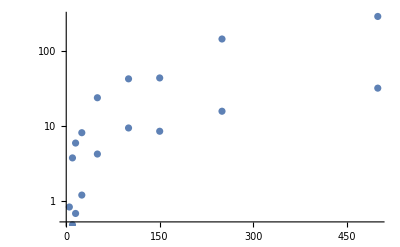

```mathematica
Show[lplot,rplot]
```

```mathematica
List@@linearDS[[4,{"Nodes Count","Separator MSE"}]]//Normal
```

{5,0.7525}

```mathematica
Length[linearDS]/Length[meansDS]
```

5

```mathematica
pointsOf[column_]:=Table[Point[List@@linearDS[[i,{"Nodes Count",column}]]//Normal],{i,1,Length[linearDS]}];
```

```mathematica
pointsOf["Separator MSE"]
```

{Point[{5,0.806}],Point[{5,0.1093}],Point[{5,1.2802}],Point[{5,0.7525}],Point[{5,1.2393}],Point[{10,5.6163}],Point[{10,1.6236}],Point[{10,1.91}],Point[{10,6.6607}],Point[{10,2.967}],Point[{15,9.2862}],Point[{15,4.0269}],Point[{15,5.8952}],Point[{15,8.6131}],Point[{15,1.7551}],Point[{25,16.1916}],Point[{25,7.8161}],Point[{25,5.0618}],Point[{25,6.1072}],Point[{25,5.3996}],Point[{50,31.2572}],Point[{50,35.2181}],Point[{50,29.1011}],Point[{50,10.3335}],Point[{50,12.2552}],Point[{100,17.0418}],Point[{100,28.2113}],Point[{100,34.5643}],Point[{100,87.2323}],Point[{100,43.5559}],Point[{150,46.664}],Point[{150,30.2776}],Point[{150,30.1979}],Point[{150,51.8355}],Point[{150,57.5102}],Point[{250,214.088}],Point[{250,86.9779}],Point[{250,86.7803}],Point[{250,102.211}],Point[{250,221.919}],Point[{500,272.165}],Point[{500,152.5}],Point[{500,354.314}],Point[{500,280.416}],Point[{500,358.871}]}

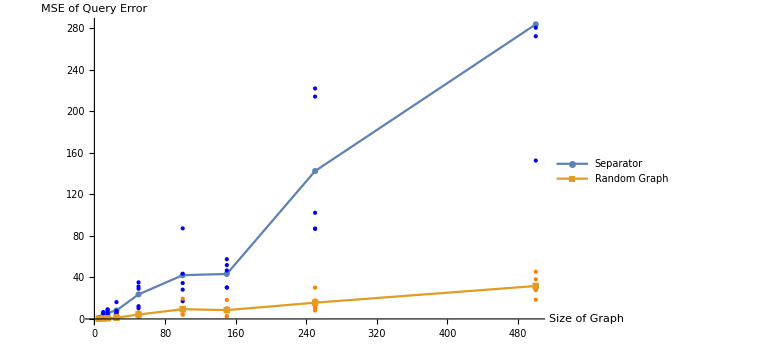

```mathematica
ListPlot[{sepValues,rndValues},PlotRange->All,PlotLegends->{"Separator","Random Graph"},AxesLabel->{"Size of Graph","MSE of Query Error"},Joined->True,PlotMarkers->Automatic,ImageSize->Large,Epilog->{Blue,PointSize[Small],pointsOf["Separator MSE"],Orange,pointsOf["Random MSE"]}]
```